# 1. Cálculo avanzado en espacios de variables reales y complejas

## Ciencia e Ingeniería de Materiales

### Materiales Metálicos

### Materiales Electrónicos

### Materiales Cerámicos

### Materiales Poliméricos

### Smart Materials, Functional Materials

A smart fluid developed in labs at the Michigan Institute of Technology 
( http://webdocs.cs.ualberta.ca/~database/MEMS/sma_mems/smrt.html )

Smart materials have one or more properties that can be dramatically altered. Most everyday materials have physical properties, which cannot be significantly altered; for example if oil is heated it will become a little thinner, whereas a smart material with variable viscosity may turn from a fluid which flows easily to a solid. A variety of smart materials already exist, and are being researched extensively.These include piezoelectric materials, magneto - rheostatic materials, electro - rheostatic materials, and shape memory alloys.

Functional materials are generally characterised as those materials which possess particular native properties and functions of their own.These can include, for example, ferroelectricity, piezoelectricity, magnetism, energy storage functions etc. Functional materials are found in all classes of materials - ceramics, metals, polymers and organic molecules.
( http://www3.imperial.ac.uk/materials/research/functionalmaterials )

### Complex Materials

### Programmable matter

Programmable matter refers to matter which has the ability to change its physical properties (shape, density, moduli, conductivity, optical properties, etc.) in a programmable fashion, based upon user input or autonomous sensing. Programmable matter is thus linked to the concept of a material which inherently has the ability to perform information processing.
( http://en.wikipedia.org/wiki/Programmable_matter )
( http://www.selfassemblylab.net/research_projects.php )

### Biomaterials

A cell - bearing structure for tissue culture, developed at UCL Mechanical Engineering by Dr Jayasinghe
( http://www.engineering.ucl.ac.uk/blog/events/our-bionic-future-the-role-of-biomaterials-in-re-engineering-the-human-body/ )

### Quantum dots materials

Quantum dots are a new class of materials, in which absorption - and emission properties can be set by adjusting particle size and particle surface passivation by means of various ligands.
(http://www.iap.fraunhofer.de/en/Forschungsbereiche/Funktionale_Polymersysteme/funktionsmaterialienundbauelemente/nanomaterialien_undquantumdots.html )

### Fullerene

## Funciones, límites y continuidad

### Funciones

Una función f es un mapeo de un conjunto, llamado el dominio de f, a otro llamado el rango de f.
Suponga que f es definida por:
f(x) = 8x (x-1)^2 + 2x
sobre el dominio D, el cual es el segmento
0.1 < x ≤ 1
del eje real.
De esta forma el rango R de la función será alguna porción del eje y.

```mathematica
f[x_]:=8 x (x-1)^2+2 x;
Plot[f[x],{x,0.1,1},AxesOrigin->{0,0},PlotRange->{{0,1},{0,2.2}}]
```

```mathematica
f[0.1]
```

```mathematica
f[1]
```

Encontramos que el rango R de la función es el segmento
0.848 < f(x) ≤ 2

De manera similar, una función f(x,y) de dos variables reales x, y, puede representarse mediante una superficie como en el siguiente ejemplo.

```mathematica
Plot3D[x^3-x  y^2,{x,-1,1},{y,-1,1}]
```

Siempre requeriremos que f sea univaluada, esto es, que a cada punto en D le corresponda un punto unicamente definido en R .
Esto incluye el caso en el que a un punto dado en el rango R le puedan corresponder más de un punto del dominio D, como en el ejemplo anterior.
En el caso en que a cada punto en R le corresponda un único punto de D, diremos que f es una función uno a uno.
La función f debe de ser uno a uno para que la función inversa x = x( f )  exista.

### Límites, continuidad y continuidad uniforme

Decimos que f(x) tiene el límite L cuando x tiende a x_0 y escribimos
lim_(x→x_0) f(x) = L
si para cada ϵ > 0 existe una δ > 0 tal que si 0 < | x - x_0 | < δ , entonces | f(x) - L | < ϵ.

#### Ejemplo 1

f(x)=Piecewise[{{x^2,, 0≤x≤4, x≠3}, {27,, x=3}}]

```mathematica
Show[Plot[x^2,{x,0,4}],ListPlot[{{3,9}},PlotMarkers->{""}],ListPlot[{{3,27}},PlotMarkers->{""}],PlotRange->All]
```

Si además de tener
lim_(x→x_0) f(x) = L
también se tiene
f(x_0) = L
decimos que f(x) es continua en x_0.
f(x) es continua en x_0, si para cada ϵ > 0 existe una δ > 0 tal que si 0 < | x - x_0 | < δ , entonces | f(x) - f(x_0) | < ϵ.

#### Ejemplo 2

H(x)=Piecewise[{{0,, x<0}, {1,, x⩾0}}]

```mathematica
Plot[UnitStep[x],{x,-3,3},PlotStyle->Thick]
```

```mathematica
Plot3D[UnitStep[x,y],{x,-3,3},{y,-3,3},Mesh->5]
```

#### Ejemplo 3

f(x)=cos(1/x)

```mathematica
a=1;
Plot[Cos[1/x],{x,-a,a}]
```

#### Ejemplo 4

f(x)=sin(x)/x

```mathematica
b=50;
Plot[Sin[x]/x,{x,-b,b},PlotRange->All]
```

```mathematica
Limit[Sin[x]/x,x->0]
```

1

Decimos que f(x) es uniformemente continua sobre D, si para cada ϵ > 0 existe una δ > 0 tal que si 0 < | x - x_0 | < δ, entonces | f(x) - f(x_0) | < ϵ, para toda x_0 en D.

### Teoremas de límites

#### Si f(x)=c, con c constante, entonces lim_(x→a) f(x)=c

Asumiendo que  lim_(x→a)  f(x)=A y  lim_(x→a)  g(x)=B

#### lim_(x→a) c f(x)= c lim_(x→a) f(x)= c A

#### lim_(x→a) [ f(x) ± g(x)]= lim_(x→a) f(x) ± lim_(x→a) g(x) = A ± B

#### lim_(x→a) [ f(x) g(x)]= lim_(x→a) f(x) lim_(x→a) g(x) = A B

#### lim_(x→a) ((f(x))/(g(x)))= (lim_(x→a) f(x))/(lim_(x→a) g(x)) = A/B, si B ≠ 0

#### lim_(x→a) (f(x))^(1/n)= lim_(x→a) (f(x))^(1/n)= A^(1/n), si A^(1/n) está definido

#### Regla de L’Hôpital

Si  lim_(x→a)   f(x) = lim_(x→a)   g(x )= 0, ó si  lim_(x→a)   f(x) = lim_(x→a)   g(x )= ± ∞
y  lim_(x→a)   (f'(x))/(g'(x)) existe, y g’(x) ≠ 0 para toda x con x≠c, entonces

 lim_(x→a)   (f(x))/(g(x))= lim_(x→a)   (f'(x))/(g'(x))

### Ejercicios de límites

#### lim_(x→2) (x^2-4)/(x-2)

```mathematica
lim_(x->2) (x^2-4)/(x-2)=lim_(x->2) ((x+2)(x-2))/(x-2)=lim_(x->2) (x+2)=4
```

#### Mostrar que: lim_(x→2) (4x-5)=3 , utilizando la definición de límite.

Elegimos ϵ > 0. Debemos de encontrar una δ > 0, tal que si 0 < |x-2| < δ entonces |(4x-5)-3| < ϵ .
Tenemos que |(4x-5)-3| = |4x-8| = 4 |x-2|.
Si tomamos δ = ϵ/4, entonces si 0 < |x-2| < δ se tiene que |(4x-5)-3| =  4 |x-2| < 4 δ = ϵ .

#### lim_(x→0) 1/x^2

```mathematica
Plot[1/x^2,{x,-1,1}]
```

#### lim_(x→0^+) 1/x ; lim_(x→0^-) 1/x

```mathematica
Plot[1/x,{x,-1,1}]
```

#### lim_(x→+∞) 1/x

```mathematica
lim_(x->+∞) 1/x=0
```

#### lim_(x→+∞) (2+1/x^2)

```mathematica
lim_(x->+∞) (2+1/x^2)=2
```

#### lim_(x→0) (1/x^2)/(1/x^4)

```mathematica
lim_(x->0) (1/x^2)/(1/x^4)=lim_(x->0) x^2=0
```

#### lim_(x→2) (2 x+3)

```mathematica
lim_(x->2) (2 x+3) =Underscript[2 lim, x->2] x+ lim_(x->2) 3= 7
```

#### lim_(x→4) √(25 - x^2)

```mathematica
lim_(x->4) √(25 - x^2)=√(lim_(x->4) (25 - x^2)) = 3
```

#### lim_(x→-5) (x^2- 25)/(x + 5)

```mathematica
lim_(x->-5) (x^2-25)/(x + 5)=lim_(x->-5) (x-5) = -10
```

#### lim_(x→4) (x - 4)/(x^2 -x - 12)

```mathematica
lim_(x->4) (x-4)/(x^2 -x - 12)=lim_(x->4) (x-4)/((x+3)(x-4))=lim_(x->4) 1/(x+3) = 1/7
```

#### lim_(h→0) ((x+h)^2- x^2)/h

```mathematica
lim_(h->0) ((x+h)^2-x^2)/h=lim_(h->0) (x^2+2hx+h^2-x^2)/h=lim_(h->0) (2hx+h^2)/h=lim_(h->0) (2x+h) = 2x
```

#### lim_(x→1) (x^2 + x - 2)/(x-1)^2

```mathematica
lim_(x->1) (x^2 + x - 2)/(x-1)^2=lim_(x->1) ((x - 1)(x + 2))/(x-1)^2=lim_(x->1) (x + 2)/(x-1)       diverge
```

```mathematica
Plot[(x^2 + x - 2)/(x-1)^2,{x,0,2}]
```

#### lim_(x→±∞) (3x - 2)/(9x + 7)

```mathematica
lim_(x->±∞) (3x - 2)/(9x + 7)=lim_(x->±∞) (3- 2/x)/(9 + 7/x)= (3-0)/(9-0) = 1/3
```

#### Dada f(x)=√(5x+1), encontrar lim_(h→0) (f(x+h)- f(x))/h para x > - 1/5

```mathematica
lim_(h->0) (f(x+h)-f(x))/h=lim_(h->0) (√(5(x+h)+1)-√(5x+1))/h=lim_(h->0) ((√(5(x+h)+1)-√(5x+1))/h)((√(5(x+h)+1)+√(5x+1))/(√(5(x+h)+1)+√(5x+1)))=lim_(h->0) (((5(x+h)+1)-(5x+1))/(h (√(5(x+h)+1)+√(5x+1))))=lim_(h->0) 5/(√(5(x+h)+1)+√(5x+1))=5/(2 √(5x+1))
```

#### lim_(x→0) (2 sin(x) - sin(2x))/(x -sin(x))

```mathematica
lim_(x->0) (2 sin(x) - sin(2x))/(x -sin(x))= lim_(x->0) (2 cos(x) -2 cos(2x))/(1 -cos(x))= lim_(x->0) (-2 sin(x) +4 sin(2x))/(sin(x))=  lim_(x->0) (-2 cos(x) +8 cos(2x))/(cos(x))=(-2+8)/1 = 6
```

### Teoremas de continuidad

Asumiendo que  f(x) y g(x) son funciones continuas en x_0

#### La función constante h(x)=c, es continua en cada x_0

#### c f(x) es continua en x_0, para cualquier constante c

#### f(x) ± g(x) es continua en x_0

#### f(x) g(x) es continua en x_0

#### (f(x))/(g(x)) es continua en x_0, si g(x_0) ≠ 0

#### (f(x))^(1/n) es continua en x_0, si (f(x_0))^(1/n) está definida

### Ejercicios de continuidad

#### f(x)=1/(x-2)

```mathematica
f(x)=1/(x-2) es discontinua en x=2,porque f(2) no está definida y también porque  lim_(x->2) f(x)  diverge.
La discontinuidad es no removible.
```

```mathematica
Plot[1/(x-2),{x,1,3}]
```

#### f(x)=(x^2-4)/(x-2)

```mathematica
f(x)=(x^2-4)/(x-2) es discontinua en x=2,porque f(2) no está definida. Sin embargo,  lim_(x->2) f(x) =  lim_(x->2) ((x+2)(x-2))/(x-2)=  lim_(x->2) (x+2)=4.
La discontinuidad es removible, porque si extendemos la función definiendo su valor en f(2)=4, entonces dicha función extendida será continua en x=2.
```

```mathematica
Plot[(x^2-4)/(x-2),{x,1,3}]
```

#### Determine el tipo de discontinuidad de: f(x)=2/x

```mathematica
Discontinuidad no removible en x=0.
```

```mathematica
Plot[1/x,{x,-1,1}]
```

#### Determine el tipo de discontinuidad de: f(x)=(x-1)/((x+3)(x-2))

```mathematica
Discontinuidades no removibles en x=-3, x=2.
```

```mathematica
Plot[(x-1)/((x+3)(x-2)),{x,-4,4}]
```

#### Determine el tipo de discontinuidad de: f(x)=(x^3-27)/(x^2-9)

```mathematica
f(x)=(x^3-27)/(x^2-9)=((x-3)(x^2+3x+9))/((x-3)(x+3))=(x^2+3x+9)/(x+3)
Discontinuidad removible en x=3.
Discontinuidad no removible en x=-3.
```

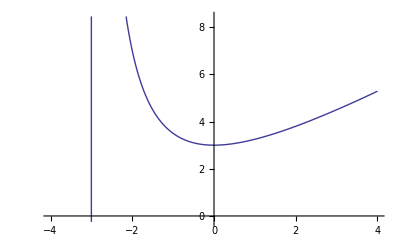

```mathematica
Plot[(x^3-27)/(x^2-9),{x,-4,4}]
```

#### Determine el tipo de discontinuidad de: f(x)=(4-x^2)/(3-√(x^2+5))

```mathematica
f(x)=(4-x^2)/(3-√(x^2+5))=(4-x^2)/(3-√(x^2+5))((3+√(x^2+5))/(3+√(x^2+5)))=3+√(x^2+5)
Discontinuidad removible en x=±2.
```

```mathematica
Plot[(4-x^2)/(3-√(x^2+5)),{x,-3,3}]
```

## Integración y diferenciación de funciones y sus expansiones en series

### La derivada

Si y=f(x) y x_0 está en el dominio de f, entonces la derivada de f en x_0 está definida como:
 lim_(Δx→0) Δy/Δx= lim_(Δx→0)   (f(x_0+Δx)-f(x_0))/Δx

Se dice que una función es diferenciable en un punto x_0, si la derivada de la función existe en ese punto.

### Ejercicios de derivadas 1

#### Encuentre dy/dxdada y=x^3-x^2-4 . Evalúe el resultado en (a) x = 4, (b) x = 0, (c) x = -1.

y + Δy = (x + Δx)^3+ (x + Δx)^2-4=x^3+3 x^2 (Δx)+3x (Δx)^2+(Δx)^3 -x^2-2x(Δx)-(Δx)^2-4  
entonces
Δy = (3 x^2-2x) (Δx)+(3x -1)(Δx)^2+(Δx)^3 ,
así
Δy/Δx= 3 x^2-2x+(3x -1)(Δx)+(Δx)^2 
dy/dx= lim_(Δx→0) Δy/Δx= lim_(Δx→0) (3 x^2-2x+(3x -1)(Δx)+(Δx)^2)=3 x^2-2x 
a) dy/dx|_(x=4)=3(4)^2-2(4)=40 
b) dy/dx|_(x=0)=3(0)^2-2(0)=0 
c) dy/dx|_(x=-1)=3(-1)^2-2(-1)=5

### Teoremas de derivación

Asumiendo que u,v y w son funciones diferenciables en x, y c, m son constantes, tenemos

#### d/dx(c)=0

#### d/dx(x)=1

#### d/dx(cu)=c du/dx

#### d/dx(u+v+...)= du/dx+dv/dx+...

#### d/dx(uv)= u dv/dx+ v du/dx

#### d/dx(u/v)= (v du/dx- u dv/dx)/v^2, si v ≠ 0

#### d/dx(1/x)= -1/x^2, si x ≠ 0

#### d/dx(x^m)=mx^(m-1)

#### d/dx(f(g(x)))=f’(g(x)) g’(x)

### Ejercicios de derivadas 2

Encuentre las diferenciales  df/dx  de:

#### f(x)= x^2 ln(x)+3x

#### f(x)= (2x-1)/(x+2)

#### f(x)= x^2 √x-5x

#### f(x)= sin((cos(x))/x)

## Integración

### Propiedades

#### ∫_a^b c f(x)dx=c∫_a^b f(x)dx

#### ∫_a^a f(x)dx=0

#### ∫_a^b f(x)dx=-∫_b^a f(x)dx

#### ∫_a^b [ f(x) ± g(x)] dx=∫_a^b f(x) dx ± ∫_a^b g(x) dx

### Cambio de variable

#### Evaluar ∫_1^9 √(5x+4)ⅆx

Consideramos u=5x+4, entonces du=5dx. Cuando x=1, u=9, y cuando x=9, u=49. Así,

 ∫_1^9 √(5x+4)ⅆx=∫_9^49 √u 1/5 ⅆu=1/5∫_9^49 u^(1/2)ⅆu=1/5(2/3 u^(3/2))|_9^49=632/15 =42.1333

### Integración por partes

∫uⅆv=uv-∫vⅆu

#### ∫x ln(x)ⅆx

u=ln(x)		dv=x dx
du=1/xdx	v=1/2 x^2

∫x ln(x)ⅆx = ∫uⅆv
 = (ln(x))(1/2 x^2)-∫1/2 x^2(1/x ⅆx) 
 = 1/2 x^2ln(x)-1/2∫xⅆx 
 = 1/2 x^2ln(x)-1/4x^2 + C
 = 1/4x^2(2 ln(x) -1) + C

#### ∫x e^x ⅆx

u=x		dv=e^x dx
du=dx		v=e^x

∫x e^x ⅆx =xe^x-∫e^x dx 
 = 1/2 x^2ln(x)-1/2∫xⅆx 
 = xe^x-e^x + C
 = e^x(x -1) + C

#### ∫e^x cos(x)ⅆx

u=e^x		dv=cos(x) dx
du=e^xdx	v=sin(x)

∫e^x cos(x)ⅆx =e^x sin(x)-∫e^x sin(x)dx ... (1)

Ahora calculamos ∫e^x sin(x)dx
u=e^x		dv=sin(x) dx
du=e^xdx	v=-cos(x)

∫e^x sin(x)ⅆx =-e^x cos(x)+∫e^x cos(x)dx ... (2)

Sustituyendo (2) en (1)
∫e^x cos(x)ⅆx =e^x sin(x)-(-e^x cos(x)+∫e^x cos(x)dx)
=e^x sin(x)+e^x cos(x)-∫e^x cos(x)dx
entonces
2∫e^x cos(x)dx=e^x sin(x)+e^x cos(x)
y finalmente
∫e^x cos(x)dx=1/2(e^x sin(x)+e^x cos(x))

### Integrandos trigonométricos tipo 1

Consideremos integrales de la forma ∫sin^k(x) cos^n(x)ⅆx, en donde k y n son enteros no-negativos.
Tipo 1. Al menos uno de sin(x) y cos(x) aparece como una potencia impar.
-Sustituir la otra función.

#### ∫sin^3(x) cos^2(x)ⅆx

u=cos(x)
du=-sin(x)dx	

⇒∫sin^3(x) cos^2(x)ⅆx=∫sin^2(x) cos^2(x)sin(x)ⅆx
                                       =∫[1-cos^2(x)] cos^2(x)sin(x)ⅆx
                                        =-∫[1-u^2] u^2 ⅆu
                                        =-∫[u^2-u^4] ⅆu
                                        =∫[u^4-u^2] ⅆu
                                        =∫u^4 ⅆu-∫u^2 ⅆu
                                        =1/5 u^5-1/3 u^3+C
                                        =1/5 cos^5(x)-1/3 cos^3(x)+C

#### ∫sin^4(x) cos^7(x)ⅆx

u=sin(x)
du=cos(x)dx	

⇒∫sin^4(x) cos^7(x)ⅆx=∫sin^4(x) cos^6(x)cos(x)ⅆx
                                       =∫(sin^4(x)[cos^2(x)])^3 cos(x)ⅆx
                                       =∫(sin^4(x)[1-sin^2(x)])^3 cos(x)ⅆx
                                        =∫(u^4[1-u^2])^3 ⅆu
                                        =∫u^4[1-3 u^2+3 u^4-u^6] ⅆu
                                      =∫[u^4-3 u^6+3 u^8-u^10] ⅆu
                                      =∫u^4 ⅆu-3∫ u^6 ⅆu+3∫u^8 ⅆu-∫u^10 ⅆu
                                         =1/5 u^5-3/7 u^7+3/9 u^9-1/11 u^11+C
                                         =1/5 sin^5(x)-3/7 sin^7(x)+3/9 sin^9(x)-1/11 sin^11(x)+C

#### ∫sin^5(x) ⅆx

u=cos(x)
du=-sin(x)dx	

⇒∫sin^5(x) ⅆx=∫sin^4(x) sin(x)ⅆx
                                       =∫[sin^2(x)]^2 sin(x)ⅆx
                                       =∫[1-cos^2(x)]^2 sin(x)ⅆx
                                        =-∫[1-u^2]^2 ⅆu
                                        =-∫[1-2 u^2+ u^4] ⅆu
                                      =-∫ ⅆu+2∫ u^2 ⅆu-∫u^4 ⅆu
                                         =-u+2/3 u^3-1/5 u^5+C
                                          =-cos(x)+2/3 cos^3(x)-1/5 cos^5(x)+C

### Integrandos trigonométricos tipo 2

Consideremos integrales de la forma ∫sin^k(x) cos^n(x)ⅆx, en donde k y n son enteros no-negativos.
Tipo 2. Ambas potencias de sin(x) y cos(x) son pares.
-Usar las identidades:
cos^2(x)=(1+cos(2x))/2
sin^2(x)=(1-cos(2x))/2

#### ∫cos^2(x) sin^4(x)ⅆx

∫cos^2(x) sin^4(x)ⅆx=∫(cos^2(x) [sin^2(x)])^2 ⅆx
                                       =∫([(1+cos(2x))/2] [(1-cos(2x))/2])^2 ⅆx
                                      =∫[(1+cos(2x))/2] [(1-2cos(2x)+cos^2(2x))/4]ⅆx
                                     =1/8∫[1-2cos(2x)+cos^2(2x)+cos(2x)-2cos^2(2x)+cos^3(2x)] ⅆx
                                     =1/8∫[1-cos(2x)-cos^2(2x)+cos^3(2x)] ⅆx
                                     =1/8[∫ⅆx-∫cos(2x) ⅆx-∫cos^2(2x)ⅆx+∫cos^3(2x)ⅆx]
                                     =1/8[x-(sin(2x))/2-∫[(1+cos(4x))/2]ⅆx+∫cos(2x)cos^2(2x)ⅆx]
                                     =1/8[x-(sin(2x))/2-1/2[x+(sin(4x))/4]+∫cos(2x)[1-sin^2(2x)]ⅆx]
                                     =1/8[1/2 x-(sin(2x))/2-(sin(4x))/8+∫cos(2x)ⅆx-∫cos(2x)sin^2(2x)ⅆx]
si u=sin(2x), entonces du=2cos(2x)
⇒∫cos^2(x) sin^4(x)ⅆx=1/8[1/2 x-(sin(2x))/2-(sin(4x))/8+(sin(2x))/2-1/2∫u^2 ⅆu]
                                                =1/8[1/2 x-(sin(4x))/8-1/6 u^3]+C
                                                =1/16 x-(sin(4x))/64-1/48 sin^3(2x)+C

### Integrandos trigonométricos tipo 3

Consideremos integrales de la forma ∫tan^k(x) sec^n(x)ⅆx, en donde k y n son enteros no-negativos.
sec^2(x)=1+tan^2(x)
Tipo 3. n es par.
-Sustituir u = tan(x).

#### ∫tan^2(x) sec^4(x)ⅆx

u=tan(x)
du=sec^2(x)dx	

⇒∫tan^2(x) sec^4(x)ⅆx=∫tan^2(x) sec^2(x)sec^2(x)ⅆx
                                       =∫tan^2(x) [1+tan^2(x)] sec^2(x)ⅆx
                                        =∫ u^2[1+u^2] ⅆu
                                        =∫[u^2+u^4] ⅆu
                                         =∫u^2 ⅆu+∫u^4 ⅆu
                                        =1/3 u^3+1/5 u^5+C
                                        =1/3 tan^3(x)+1/5 tan^5(x)+C

### Integrandos trigonométricos tipo 4

Consideremos integrales de la forma ∫tan^k(x) sec^n(x)ⅆx, en donde k y n son enteros no-negativos.
sec^2(x)=1+tan^2(x)
Tipo 4. n es impar y k es impar.
-Sustituir u = sec(x).

#### ∫tan^3(x) sec(x)ⅆx

u=sec(x)
du=sec(x)tan(x)dx	

⇒∫tan^3(x) sec(x)ⅆx=∫tan^2(x) sec(x)tan(x)ⅆx
                                     =∫[sec^2(x)-1]  sec(x)tan(x)ⅆx
                                        =∫ [u^2-1] ⅆu
                                          =∫u^2 ⅆu-∫ ⅆu
                                        =1/3 u^3-u+C
                                        =1/3 sec^3(x)-sec(x)+C

### Integrandos trigonométricos tipo 5

Consideremos integrales de la forma ∫tan^k(x) sec^n(x)ⅆx, en donde k y n son enteros no-negativos.
sec^2(x)=1+tan^2(x)
Tipo 4. n es impar y k es par.

#### ∫tan^2(x) sec(x)ⅆx

⇒∫tan^2(x) sec(x)ⅆx=∫[sec^2(x)-1] sec(x)ⅆx
                                     =∫[sec^3(x)- sec(x)] ⅆx
                                      =1/2[sec(x)tan(x)+ln|sec(x)+tan(x)|]-ln|sec(x)+tan(x)|+C
                                      =1/2[sec(x)tan(x)-ln|sec(x)+tan(x)|]+C

### Integrandos trigonométricos tipo 6

Consideremos integrales de la forma ∫sin(Ax) cos(Bx)ⅆx, ∫sin(Ax) sin(Bx)ⅆx, y ∫cos(Ax) cos(Bx)ⅆx.
Usaremos sin(Ax) cos(Bx)=1/2{sin([A+B]x)+sin([A-B]x)}
sin(Ax) sin(Bx)=1/2{cos([A-B]x)-cos([A+B]x)}
cos(Ax) cos(Bx)=1/2{cos([A-B]x)+cos([A+B]x)}

#### ∫sin(7x) cos(3x)ⅆx

⇒∫sin(7x) cos(3x)ⅆx=∫1/2{sin([7+3]x)+sin([7-3]x)}ⅆx
                                     =∫1/2{sin(10x)+sin(4x)}ⅆx
                                     =1/2∫sin(10x)ⅆx+1/2∫sin(4x)ⅆx
                                     =-1/20cos(10x)-1/8 cos(4x)+C

#### ∫sin(7x) sin(3x)ⅆx

⇒∫sin(7x) sin(3x)ⅆx=∫1/2{cos([7-3]x)-cos([7+3]x)}ⅆx
                                     =∫1/2{cos(4x)-cos(10x)}ⅆx
                                     =1/2∫cos(4x)ⅆx-1/2∫cos(10x)ⅆx
                                     =1/8 sin(4x)-1/20 sin(10x)+C

#### ∫cos(7x) cos(3x)ⅆx

⇒∫cos(7x) cos(3x)ⅆx=∫1/2{cos([7-3]x)+cos([7+3]x)}ⅆx
                                     =∫1/2{cos(4x)+cos(10x)}ⅆx
                                     =1/2∫cos(4x)ⅆx+1/2∫cos(10x)ⅆx
                                     =1/8 sin(4x)+1/20 sin(10x)+C

### Sustituciones trigonométricas tipo 1

Si √(a^2+x^2) aparece en el integrando.
-Sustituir  x = a tan(θ).

#### ∫ⅆx/(x^2 √(4 + x^2))

x = 2 tan(θ), entonces θ=tan^-1(x/2)
dx=2sec^2(θ)dθ
y
√(4 + x^2)=√(4 + 4tan^2(θ))=2 √(1 + tan^2(θ))=2 √(sec^2(θ))=2|sec(θ)|	
Por la definición de la cotangente, -π/2<θ<π/2. Así, sec(θ)>0
⇒√(4 + x^2)=2sec(θ)

⇒∫ⅆx/(x^2 √(4 + x^2))=∫(2sec^2(θ)dθ)/((2tan(θ))^2 2sec(θ))
                          =∫(sec(θ)dθ)/(4tan^2(θ))
                         =1/4∫(cos(θ)dθ)/(sin^2(θ))
                         =1/4∫sin^-2(θ)cos(θ)dθ
                        =1/4[-(sin(θ))^-1]+C
                        =- 1/(4sin(θ))+C
y como
sin(θ)=(tan(θ))/(sec(θ))=(2x)/(2 √(4 + x^2))=x/(√(4 + x^2))

⇒∫ⅆx/(x^2 √(4 + x^2))=- (√(4 + x^2))/(4x)+C

```mathematica
Plot[Tan[θ],{θ,-2π/2,2π/2}]
```

```mathematica
Plot[Sec[θ],{θ,-π/2,π/2}]
```

### Sustituciones trigonométricas tipo 2

Si √(a^2-x^2) aparece en el integrando.
-Sustituir  x = a sin(θ).

#### ∫ⅆx/(x^2 √(9 - x^2))

x = 3 sin(θ), entonces θ=sin^-1(x/3)
dx=3cos(θ)dθ
y
√(9 - x^2)=√(9 - 9sin^2(θ))=3 √(1 - sin^2(θ))=3 √(cos^2(θ))=3|cos(θ)|	
Por la definición del inverso del seno, -π/2<θ<π/2. Así, cos(θ)>0
⇒√(9 - x^2)=3cos(θ)

⇒∫ⅆx/(x^2 √(9 - x^2))=∫(3cos(θ)dθ)/((3sin(θ))^2 3cos(θ))
                          =∫dθ/(9sin^2(θ))
                         =1/9∫dθ/(sin^2(θ))
                         =1/9∫csc^2(θ)dθ
                        =-1/9cot(θ)+C
                        =- (cos(θ))/(9sin(θ))+C
                        =- (3 √(9 - x^2))/(27x)+C
⇒∫ⅆx/(x^2 √(4 + x^2))=- (√(9 - x^2))/(9x)+C

```mathematica
Plot[Cos[θ],{θ,-π/2,π/2}]
```

### Sustituciones trigonométricas tipo 3

Si √(x^2-a^2) aparece en el integrando.
-Sustituir  x = a sec(θ).

#### ∫(x^2 ⅆx)/(√(x^2 - 4))

x = 2 sec(θ), entonces θ=sec^-1(x/2)
dx=2sec(θ)tan(θ)dθ
y
√(x^2 - 4)=√((2sec(θ))^2 - 4)=2 √((sec(θ))^2 - 1)=2 √(tan^2(θ))=2|tan(θ)|	
Por la definición del inverso de la secante, θ está en el primer y tercer cuadrante. Así, tan(θ)>0
⇒√(x^2 - 4)=2tan(θ)

⇒∫(x^2 ⅆx)/(√(x^2 - 4))=∫([2sec(θ)]^2 2sec(θ)tan(θ)dθ)/(2tan(θ))
                          =∫[2sec(θ)]^2 sec(θ)dθ
                         =4∫sec^3(θ)dθ
                         =2[sec(θ)tan(θ)+ln|sec(θ)+tan(θ)|+C]
                        =2[x/2 1/2 √(x^2 - 4)+ln|x/2+1/2 √(x^2 - 4)|]
                       =x/2 √(x^2 - 4)+2ln|x/2+1/2 √(x^2 - 4)|+C

```mathematica
Plot[Sec[θ],{θ,-2π,2π}]
```

```mathematica
Plot[Tan[θ],{θ,0,π/2}]
```

```mathematica
Plot[Tan[θ],{θ,π,3π/2}]
```

### Integración por fracciones parciales

Consideremos integrales de la forma ∫(N(x))/(D(x)) ⅆx, en donde N(x) y D(x) son polinomios.
Una función (N(x))/(D(x)) se denomina función racional.
Asumimos las siguientes restricciones:

(i) El coeficiente del término con la mayor potencia de x en D(x), es +1.
(ii) N(x) es de grado menor que D(x).

Un cociente (N(x))/(D(x)) que satisface (ii) se llama una función racional propia.
Se dice que un polinomio es irreducible si no se puede expresar como el producto de dos polinomios de grado más bajo.

Cualquier polinomio lineal f(x)=a x +b es irreducible, dado que los polinomios de grado menor que f(x) son constantes, y f(x) no es el producto de dos constantes.

Consideremos un polinomio cuadrático g(x)=a x^2 + bx + c.
Entonces, g(x) es irreducible si y sólo si  b^2 -4 a c<0.

Para ver esto, asumimos que g(x) es reducible. Entonces g(x)=(A x+B)(C x+D). 
De aquí, x=-B/A x=-D/C  son raíces de  g(x).
La fórmula cuadrática
 x=(-b±√(b^2-4a c))/(2a),
 debe de dar dichas raíces. Por lo tanto, b^2-4 a c no puede ser negativo.
 
 Por otro lado, asumimos que  b^2-4 a c≥0. Entonces la fórmula cuadrática nos da las dos raíces de g(x).
 Pero si r es una raíz de g(x), entonces g(x) es divisible por  x-r.
 De aquí, g(x) es reducible.

#### x^2 + 4 es irreducible , dado que b^2-4 a c=-16<0.

#### x^2+ x - 4 es reducible , dado que b^2-4 a c=17≥0.

Teorema. Cualquier polinomio D(x) con coeficiente principal 1, puede expresarse como un producto de factores lineales de la forma  x-a  y de factores cuadráticos irreducibles de la forma  x^2 + bx + c .

#### x^3- 4x=x (x^2- 4)=x (x- 2) (x+2)

#### x^3+ 4x=x (x^2+ 4)

#### x^4- 9=(x^2- 3) (x^2+ 3)=(x- √3)(x- √3) (x^2+ 3)

### Método de Fracciones Parciales

Consideremos integrales de la forma ∫(N(x))/(D(x)) ⅆx, en donde (N(x))/(D(x)) es función racional propia.
y D(x) tiene coeficiente principal 1.
Primero se escribe D(x) como un producto de factores lineales y cuadráticos irreducibles.
El método dependerá de dicha factorización.
Consideraremos varios casos.

#### Caso I

D(x) es un producto de distintos factores lineales.

Regla
Represente el integrando como una suma de términos de la forma A/(x - a) para cada factor lineal  x-a del denominador, en donde A es una constante desconocida. Resuelva para las constantes. La integración dará una suma de términos de la forma  A ln|x-a|.

#### ∫ⅆx/(x^2 - 4)

D(x)=x^2 - 4= (x- 2) (x+2).	
Entonces
1/(x^2 - 4)=1/((x- 2) (x+2))=A/(x- 2)+B/(x+2).
A y B son constantes por determinar.
⇒1/((x- 2) (x+2))(x- 2) (x+2)=(A/(x- 2)+B/(x+2))(x- 2) (x+2)
1=A(x+2)+B(x- 2)
Sustituimos x=-2, entonces B=-1/4.
Sustituimos x=2, entonces A=1/4.
Así,
1/(x^2 - 4)=1/4(1/(x- 2)-1/(x+2))
⇒∫ⅆx/(x^2 - 4)=1/4∫(1/(x- 2)-1/(x+2))ⅆx
                      =1/4∫1/(x- 2)ⅆx-1/4∫1/(x+2)ⅆx
                      =1/4 ln|x-2|-1/4 ln|x+2|+C
                      =1/4 ln|(x-2)/(x+2)|+C

#### ∫((x + 1)ⅆx)/(x^3+ x^2 - 6 x)

D(x)=x^3+ x^2 - 6 x=x  (x^2+x- 6)=x (x-2)(x+3).	
Entonces
(x + 1)/(x^3+ x^2 - 6 x)=1/(x (x-2)(x+3))=A/x+B/(x- 2)+C/(x+3).
A, B y C son constantes por determinar.
⇒1/(x (x-2)(x+3))x (x-2)(x+3)=(A/x+B/(x- 2)+C/(x+3))x (x-2)(x+3)
1=A(x-2)(x+3)+B x (x+3) + C x (x-2)
Sustituimos x=0, entonces A=-1/6.
Sustituimos x=2, entonces B=3/10.
Sustituimos x=-3, entonces C=-2/15.
Así,
(x + 1)/(x^3+ x^2 - 6 x)=(-1/6 1/x+3/10 1/(x- 2)-2/15 1/(x+3))
⇒∫(x + 1)/(x^3+ x^2 - 6 x)ⅆx=∫(-1/6 1/x+3/10 1/(x- 2)-2/15 1/(x+3))ⅆx
                      =-1/6∫1/x ⅆx+3/10∫1/(x- 2)ⅆx-2/15∫1/(x+3)ⅆx
                      =-1/6ln|x|+3/10 ln|x-2|-2/15 ln|x+3|+C

#### Caso II

D(x) es un producto de factores lineales, alguno de los cuales ocurre más de una vez.

Regla
Por cada factor lineal  x-r que ocurre en el denominador, represente parte del integrando como  A_1/(x - r)+A_2/(x - r)^2+…+A_k/(x - r)^k. Cada factor lineal que ocurre sólo una vez se maneja como en el caso I.

#### ∫((3x + 5)ⅆx)/(x^3- x^2 - x + 1)

D(x)=x^3- x^2 -  x + 1= (x+1)(x-1)^2.	
Entonces
(3x + 5)/(x^3- x^2 -  x + 1)=A/(x+1)+B/(x- 1)+C/(x-1)^2.
A, B y C son constantes por determinar.
⇒(3x + 5)/(x^3- x^2 -  x + 1)(x+1)(x-1)^2=(A/(x+1)+B/(x- 1)+C/(x-1)^2)(x+1)(x-1)^2

(3x + 5)=A (x-1)^2+B (x+1)(x-1) + C (x+1)… (1)

Sustituimos x=1, entonces C=4.
Sustituimos x=-1, entonces A=1/2.
Para encontrar B, comparamos los coeficientes de x^2en ambos lados de la Ec. (1).
Encontramos que 0 x^2=(A+B)x^2, entonces 0=A+B, por lo que B=-1/2.
Así,
(3x + 5)/(x^3- x^2 -  x + 1)=1/2 1/(x+1)-1/2 1/(x- 1)+4 1/(x-1)^2
⇒∫(3x + 5)/(x^3- x^2 -  x + 1)ⅆx=1/2 ln|x+1|-1/2 ln|x-1|+4∫1/(x-1)^2 ⅆx
                      =1/2 ln|(x+1)/(x-1)|-4/(x- 1)+C

#### ∫((x + 1)ⅆx)/((x^3(x-2))^2)

Representamos el integrado como:
(x + 1)/((x^3(x-2))^2)=A/x+B/x^2+C/x^3+D/(x-2)+E/(x-2)^2.

⇒(x + 1)/((x^3(x-2))^2)(x^3(x-2))^2=(A/x+B/x^2+C/x^3+D/(x-2)+E/(x-2)^2)(x^3(x-2))^2
⇒(x + 1)=A (x^2(x-2))^2+B x (x-2)^2 + C (x-2)^2 +D x^3(x-2)+ E x^3

Sustituimos x=0, entonces C=1/4.
Sustituimos x=2, entonces E=3/8.
Comparamos los coeficientes de x. Encontramos que 1x=(4B - 4C)x, entonces B=1/2.
Comparamos los coeficientes de x^2. Encontramos que 0 x^2=(4 A- 4B + 4C)x^2, entonces A=1/4.
Comparamos los coeficientes de x^4. Encontramos que 0 x^4=(A+ D)x^4, entonces D=-1/4.
Así,
(x + 1)/((x^3(x-2))^2)=1/4 1/x+1/2 1/x^2+1/4 1/x^3-1/4 1/(x-2)+3/8 1/(x-2)^2
⇒∫(x + 1)/((x^3(x-2))^2)ⅆx=1/4 ln|x|-1/2 1/x-1/8 1/x^2-1/4 ln|x-2|-3/8 1/(x-2)+C
                      =1/4 ln|x/(x-2)|-(4x+1)/(8 x^2)-3/8 1/(x-2)+C

#### Caso III

D(x) es un producto de uno o más factores cuadráticos irreducibles distintos, y posiblemente también de algunos factores lineales (que pueden ocurrir más de una vez).

Regla
Los factores lineales se manejan como en los casos I y II. Por cada factor cuadrático irreducible  x^2 + bx + c, se escribe un término (A x + B)/(x^2 + b x+c) en la expresión del integrando.

#### ∫((x - 1)ⅆx)/(x (x^2+ 1)(x^2+ 2))

Representamos el integrado como:
(x - 1)/(x (x^2+ 1)(x^2+ 2))=A/x+(B x + C)/(x^2 + 1)+(D x + E)/(x^2 + 2).

⇒(x - 1)/(x (x^2+ 1)(x^2+ 2))x (x^2+ 1)(x^2+ 2)=(A/x+(B x + C)/(x^2 + 1)+(D x + E)/(x^2 + 2))x (x^2+ 1)(x^2+ 2)
⇒x - 1=A (x^2+ 1)(x^2+ 2)+(B x + C)x (x^2+ 2)+(D x + E)x (x^2+ 1)
⇒x - 1=(A +B + D)x^4+(B  + E)x^3+(3A+C+D)x^2+(2C+E)x +2A

Comparando coeficientes tenemos:
 2A=-1,    2C+E=1,    3A+C+D=0,    B  + E=0,    A +B + D=0.
 Entonces A=-1/2, B=-1, C=0, D=3/2, E=1.
Así,
(x - 1)/(x (x^2+ 1)(x^2+ 2))=-1/2 1/x-x/(x^2 + 1)+1/2(3 x + 2)/(x^2 + 2)
⇒∫(x - 1)/(x (x^2+ 1)(x^2+ 2))ⅆx=-1/2ln|x|-∫x/(x^2 + 1)ⅆx+1/2∫(3 x + 2)/(x^2 + 2)ⅆx
                                              =-1/2ln|x|+1/4 ln(x^2+1)+(√2)/2 tan^-1(x/(√2))+C

#### Caso IV

D(x) es un producto de cero o más factores lineales y uno o más factores cuadráticos irreducibles.

Regla
Los factores lineales se manejan como en los casos I y II. Por cada factor cuadrático irreducible  x^2 + bx + c  que aparece a la k-ésima potencia,  escribe términos (A_1 x + B_1)/(x^2 + b x+c)+(A_2 x + B_2)/((x^2 + b x+c)^2)+⋯(A_k x + B_k)/((x^2 + b x+c)^k) en la expresión del integrando.

#### ∫((2 x^2+ 3)ⅆx)/((x^2+ 1)^2)

Representamos el integrado como:
(2 x^2+ 3)/((x^2+ 1)^2)=(A x + B)/(x^2 + 1)+(C x + D)/((x^2 + 1)^2).

⇒(2 x^2+ 3)/((x^2+ 1)^2)(x^2+ 1)^2=((A x + B)/(x^2 + 1)+(C x + D)/((x^2 + 1)^2))(x^2+ 1)^2
⇒2 x^2+ 3= (A x + B)(x^2+1)+(C x + D)
⇒2 x^2+ 3=A x^3+B x^2+(A+C)x +(B+ D)

Comparando coeficientes tenemos:
A=0, B=2, C=0, D=1.
Así,
⇒∫(2 x^2+ 3)/((x^2+ 1)^2)ⅆx=∫2/(x^2 + 1)ⅆx+∫1/((x^2 + 1)^2)ⅆx
                                              =2tan^-1(x)+∫1/((x^2 + 1)^2)ⅆx
La integral es, haciendo x=tan(θ),
∫1/((x^2 + 1)^2)ⅆx=∫(sec^2(θ))/(sec^4(θ))ⅆθ=∫cos^2(θ)ⅆθ
                            =1/2(θ+sin(θ)cos(θ))
                            =1/2(θ+(tan(θ))/(tan^2(θ)+1))
                            =1/2(tan^-1(x)+x/(x^2+1))
Así,
⇒∫(2 x^2+ 3)/((x^2+ 1)^2)ⅆx=2tan^-1(x)+1/2(tan^-1(x)+x/(x^2+1))
                                    =5/2 tan^-1(x)+1/2 x/(x^2+1)+C